# Frustrated Internal Reflection of Twisted Light M.T. Lusk

## Introduction and Some Light Basics: Must Run

Plane waves of TE and TM polarization are incident on a sequence of parallel planar boundaries. When the angle of incidence causes total internal reflection at the first interface, the evanescent wave in the second region still couples radiation to the third region. This results in propagating waves in the third region. Both polarizations are considered here, and the combination can be used to predict the optical coupling of twisted light.

The units in this analysis are left general. All that matters is that the units of distance are 1/k_1 for all three regions. For example, if the incident light is 1.0 eV and ϵ = 4, the characteristic length is 97 nm as shown below. The value of L (layer thickness) used to illustrate the optical coupling is L = 4, and this would therefore correspond to about 400 nm of separation.

E0 = ℏ ω = ℏ c k = (ℏ c_0 k)/(√ϵ)

so

k = (E0 √ϵ)/(ℏ c_0)

```mathematica
eV = 1.6022*10^-19;
c0 = 2.99792*10^8;
hbar =6.58211928 *10^-16;(* eV-sec *)
h = 6.626068*10^-34;

ev$nm[λnm_]=(c0 h)/λnm*10^9/eV (* input wavelength in nm, output energy in eV *) ;

k$ev[energy_,ϵ_]=1/(((c0/√ϵ) hbar)/energy*10^9) (* input energy in eV and get output in inverse nm *);

CharLength[energy_,ϵ_]=1/k$ev[energy,ϵ]   (* input energy in eV and get output of characteristic length in nm *)
```

k =(ω √ϵ)/c_0

Ratio of k-magnitudes given by

```mathematica
CharLength[energy,ϵ2]/CharLength[energy,ϵ1]
```

```mathematica
CharLength[1.0,4]
```

```mathematica
CharLength[ev$nm[λnm],ϵ]
```

```mathematica
1./(2 π)
```

There is a second issue should be emphasized. The jump conditions for TE and TM polarization are different, so twisted light should exhibit an optical coupling that oscillates with the period of the Poynting vector.

-Graphics-

(Figure above is Optical_Coupling.pdf)

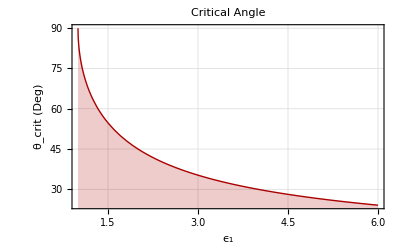

## Plotting Tools: Run this first

```mathematica
Clear[font,coloredfont];
font[name_,size_]:=Style[name,FontFamily->"Tahoma",FontSize->size,Bold]

coloredfont[name_,size_,color_]:=Style[name,FontFamily->"Helvetica",FontSize->size,Bold, color]
```

## Theory: Interface Jump Conditions

References: Many websites, demos and images of this.

Also see [Reflection_Transmission.pdf] eqs 1255 - 1259 and 1272 - 1273.

Note that index of refraction, n = √ϵ.

Maxwell’s equations in k-space:

-k⃗×H⃗ = ω D⃗

k⃗×E⃗ =ω B⃗

∇·D⃗ =0

∇·B⃗ =0

Constitutive Relations:

D⃗ =ϵ ϵ_0 E⃗

B⃗ =μ μ_0 H⃗

Interface jump conditions:

n̂×⟦E⃗⟧=OverVector[0]

⟦D⃗⟧·n̂=0

n̂×⟦H⃗⟧=OverVector[0]

⟦B⃗⟧·n̂=0

Convert to E⃗ and B⃗ keeping in mind that materials are nonmagnetic. Use k⃗= k k̂ and c = ω/k ≡ 1/√(μ μ_0 ϵ ϵ_0). Therefore

k =(ω √ϵ)/c_0

-k̂×B⃗ =(ϵ ϵ_0 μ μ_0)/(√(μ ϵ μ_0 ϵ_0)) E⃗  ≡(√ϵ)/c_0 E⃗

k̂×E⃗ =c_0/(√ϵ) B⃗

∇·E⃗ =0

∇·B⃗ =0

n̂×⟦E⃗⟧=OverVector[0]

⟦ϵ E⃗⟧·n̂=0

n̂×⟦B⃗⟧=OverVector[0]

⟦B⃗⟧·n̂=0

Use Maxwell’s equations to re-express jump conditions in terms of only E⃗:

n̂×⟦E⃗⟧=OverVector[0]

⟦ϵ E⃗⟧·n̂=0

n̂×⟦√ϵ k̂×E⃗⟧=OverVector[0]

⟦√ϵ k̂×E⃗⟧·n̂=0

### TE Polarization

E⃗ = E ŷ    and k⃗= k_x x̂ + k_z ẑ  and   n̂ ≡ ẑ

```mathematica
kcrossE = Det[{{x̂, ŷ, ẑ},{kx, 0, kz},{0,Ey,0}}]
```

```mathematica
ncross$kcrossE=Det[{{x̂, ŷ, ẑ},{0,0,1},{-Ey kz,0,Ey kx}}]
```

Interface jump conditions:

⟦E_y⟧=0

0=0

⟦√ϵ E_y(k̂)_z⟧=0

0=0

### TM Polarization

E⃗ = E_x x̂ + E_z ẑ    and     k⃗= k_x x̂ + k_z ẑ   and   n̂ ≡ ẑ

```mathematica
ncrossE = Cross[{0,0,1},{Ex,0,Ez}]
```

```mathematica
kcrossE = Cross[{kx, 0, kz},{Ex,0,Ez}]
```

```mathematica
ncross$kcrossE=Simplify[√ϵ Cross[{0,0,1},kcrossE]]
```

Interface jump conditions:

⟦E_x⟧=0

⟦ϵ E_z⟧=0

⟦√ϵ (E_z k_x-E_x k_z)⟧=0

0=0

## Fresnel Equations for a Single Planar Interface

### TE Polarization: Derivation of E-field Terms

⟦E_y⟧=0

⟦√ϵ E_y(k̂)_z⟧=0

E(r⃗, t) = E ⅇ^(ⅈ (k⃗·r⃗-ω t))ŷ

Evaluate jump conditions at x = y = z = 0 and t = 0.

```mathematica
Clear[θ,θ2,ϵ1,ϵ2,ki1,kr1,kt1,rvec];
θ2[θ_,ϵ1_,ϵ2_]=ArcSin[√(ϵ1/ϵ2)Sin[θ]]; (* Snell *)

ki1[θ_,ϵ1_,ϵ2_]={Sin[θ],0,Cos[θ]};
kr1[θ_,ϵ1_,ϵ2_]={Sin[θ],0,-Cos[θ]};
kt1[θ_,ϵ1_,ϵ2_]=√(ϵ2/ϵ1){Sin[θ2[θ,ϵ1,ϵ2]],0,Cos[θ2[θ,ϵ1,ϵ2]]};

rvec[x_,y_,z_]={x,y,z};
```

```mathematica
Clear[ErB1,EtB1];

sol=Solve[{
1 + ErB1 ==EtB1,
√ϵ1(1 -ErB1) Cos[θ1] == √ϵ2(EtB1 )Cos[θ2]

},{ErB1, EtB1}]
```

```mathematica
Clear[EtB1$TE];

ErB1$TE[θ_,ϵ1_,ϵ2_] = Simplify[ErB1 /. sol[[1]] /. {θ1->θ, θ2->θ2[θ,ϵ1,ϵ2], θ3->θ3[θ,ϵ1,ϵ2]}];

EtB1$TE[θ_,ϵ1_,ϵ2_] = Simplify[EtB1 /. sol[[1]]  /. {θ1->θ, θ2->θ2[θ,ϵ1,ϵ2], θ3->θ3[θ,ϵ1,ϵ2]}];
```

```mathematica
Simplify[ErB1$TE[θ,ϵ1,n^2 ϵ1],{n>0,ϵ1>0}]
```

Construct spatially varying electric field. The time-varying component, ⅇ^(-ⅈ ω t), is left out, since each term has this. The incident wave is given a magnitude of 1.

```mathematica
Clear[EiB1$TE$func,ErB1$TE$func,EtB1$TE$func];

EiB1$TE$func[θ_,ϵ1_,ϵ2_,x_,z_,L_]=Exp[ⅈ ki1[θ,ϵ1,ϵ2].rvec[x,0,z]];
ErB1$TE$func[θ_,ϵ1_,ϵ2_,x_,z_,L_]=ErB1$TE[θ,ϵ1,ϵ2]Exp[ⅈ kr1[θ,ϵ1,ϵ2].rvec[x,0,z]];
EtB1$TE$func[θ_,ϵ1_,ϵ2_,x_,z_,L_]=EtB1$TE[θ,ϵ1,ϵ2]Exp[ⅈ kt1[θ,ϵ1,ϵ2].rvec[x,0,z]];
```

```mathematica
ki1[θ,ϵ1,ϵ2]

Simplify[kt1[θ,ϵ1,ϵ2],{ϵ1>0,ϵ2>0}]
```

### TM Polarization: Derivation of E-field Terms

TM Polarization:

⟦E_x⟧=0

⟦ϵ E⃗⟧·n̂=0

n̂×⟦√ϵ k̂×E⃗⟧=OverVector[0]

As shown below, the second and third interface conditions are equivalent by virtue of Snell’s Law. Alternatively, and more accurately, it should be noted that the second equation gives Snell’s Law in the first place.

E_i(r⃗, t) =  E_i Cos[θ] ⅇ^(ⅈ (k⃗·r⃗-ω t))x̂ + E_i Sin[θ] ⅇ^(ⅈ (k⃗·r⃗-ω t))ẑ

E_r(r⃗, t) =  E_r Cos[θ] ⅇ^(ⅈ (k⃗·r⃗-ω t))x̂ -  E_r Sin[θ] ⅇ^(ⅈ (k⃗·r⃗-ω t))ẑ

E_t(r⃗, t) =  E_t Cos[θ_2] ⅇ^(ⅈ (k⃗·r⃗-ω t))x̂ -  E_t Sin[θ_2] ⅇ^(ⅈ (k⃗·r⃗-ω t))ẑ

```mathematica
Clear[θ,θ2,ϵ1,ϵ2,ki1,kr1,kt1,rvec];
θ2[θ_,ϵ1_,ϵ2_]=ArcSin[√(ϵ1/ϵ2)Sin[θ]];

ki1[θ_,ϵ1_,ϵ2_]={Sin[θ],0,Cos[θ]};
kr1[θ_,ϵ1_,ϵ2_]={Sin[θ],0,-Cos[θ]};
kt1[θ_,ϵ1_,ϵ2_]=√(ϵ2/ϵ1){Sin[θ2[θ,ϵ1,ϵ2]],0,Cos[θ2[θ,ϵ1,ϵ2]]};

rvec[x_,y_,z_]={x,y,z};
```

Evaluate jump conditions at x = y = z = 0 and t = 0.

```mathematica
Simplify[Cross[{0,0,1},Ei{Cos[θ1],0,Sin[θ1]}]]

Simplify[Cross[{0,0,1},Er{Cos[θ1],0,-Sin[θ1]}]]
```

Consider the first interface condition:

⟦E_x⟧=0

```mathematica
Simplify[Ei{Cos[θ1],0,Sin[θ1]}.{1,0,0}]

Simplify[ Er{Cos[θ1],0,-Sin[θ1]}.{1,0,0}]
```

The first interface condition is therefore (Eq 1270)

(E_i+E_r)Cos[θ_1] = E_t Cos[θ_2]

Consider the second interface condition:

⟦ϵ E⃗⟧·n̂=0

```mathematica
Simplify[ϵ Ei{Cos[θ1],0,Sin[θ1]}.{0,0,1}]

Simplify[ϵ Er{Cos[θ1],0,-Sin[θ1]}.{0,0,1}]
```

The condition therefore implies that

ϵ_1 Sin[θ_1](E_i-E_r) = ϵ_2 Sin[θ_2] E_t

But Snell tells us that

√ϵ1 Sin[θ1]=√ϵ2 Sin[θ2]

The second interface condition is therefore (Eq 1269)

√ϵ_1(E_i-E_r) = √ϵ_2 E_t

Now consider the third interface condition:

n̂×⟦√ϵ k̂×E⃗⟧=OverVector[0]

```mathematica
Simplify[Cross[{0,0,1},Cross[√ϵ ki1[θ1,ϵ1,ϵ2],Ei{Cos[θ1],0,Sin[θ1]}]]]

Simplify[Cross[{0,0,1},Cross[√ϵ kr1[θ1,ϵ1,ϵ2],Er{Cos[θ1],0,-Sin[θ1]}]]]
```

The third interface condition is therefore that (Eq 1269)

√ϵ_1(E_i-E_r) = √ϵ_2 E_t

The second and third interface conditions are therefore identical.

```mathematica
Clear[ErB1,EtB1];

sol=Simplify[Solve[{
(1  + ErB1 )Cos[θ1] == EtB1 Cos[θ2],
√ϵ1(1- ErB1 )==√ϵ2 EtB1
},{ErB1, EtB1}]]
```

```mathematica
Clear[EtB1$TM];

ErB1$TM[θ_,ϵ1_,ϵ2_] = FullSimplify[ErB1 /. sol[[1]] /. {θ1->θ, θ2->θ2[θ,ϵ1,ϵ2]}]

EtB1$TM[θ_,ϵ1_,ϵ2_] = FullSimplify[EtB1 /. sol[[1]]  /. {θ1->θ, θ2->θ2[θ,ϵ1,ϵ2]}];
```

```mathematica
T1=Simplify[EtB1$TM[θ,ϵ1,ϵ1 n^2] ,{ϵ1>0,n>0}]

T2=Simplify[EtB1$TE[θ,ϵ1,ϵ1 n^2] ,{ϵ1>0,n>0}]
```

Construct spatially varying electric field. The time-varying component, ⅇ^(-ⅈ ω t), is left out, since each term has this. The incident wave is given a magnitude of 1.

```mathematica
Clear[EiB1$TM$func,ErB1$TM$func,EtB1$TM$func];

EiB1$TM$func[θ_,ϵ1_,ϵ2_,x_,z_,L_]=Exp[ⅈ ki1[θ,ϵ1,ϵ2].rvec[x,0,z]];
ErB1$TM$func[θ_,ϵ1_,ϵ2_,x_,z_,L_]=ErB1$TM[θ,ϵ1,ϵ2]Exp[ⅈ kr1[θ,ϵ1,ϵ2].rvec[x,0,z]];
EtB1$TM$func[θ_,ϵ1_,ϵ2_,x_,z_,L_]=EtB1$TM[θ,ϵ1,ϵ2]Exp[ⅈ kt1[θ,ϵ1,ϵ2].rvec[x,0,z]];
```

### Demonstration Application

```mathematica
Clear[p$TE$contours];


xmax = 10;xmin = -xmax;
zmax = 5;zmin = -zmax;


p$boundary=Show[Graphics[{White,Thickness[.01],Line[{{0,xmin},{0,xmax}}]}]];

θset = 35 Degree;
ϵ1set = 4.0; ϵ2set = 1.0;

p$TE$contours = ContourPlot[If[z<=0,Re[EiB1$TE$func[θset,ϵ1set,ϵ2set,x,z,Lset]],Re[EtB1$TE$func[θset,ϵ1set,ϵ2set,x,z,Lset]]],{z,zmin,zmax},{x,xmin,xmax},Contours->20,ColorFunction->"TemperatureMap",PlotRange->All,FrameLabel->{font["z",14],font["x",14]},PlotLabel->coloredfont["TE Polarization",14,Blue],PlotPoints->100];

Show[p$TE$contours,p$boundary]
```

```mathematica
θ2[θset,ϵ1set,ϵ2set]
```

```mathematica
Clear[p$TE$contours];

p$boundary=Show[Graphics[{White,Thickness[.01],Line[{{0,-5},{0,5}}]}]];

Plot3D[If[z<=0,Re[EiB1$TE$func[θset,ϵ1set,ϵ2set,x,z,Lset]],Re[EtB1$TE$func[θset,ϵ1set,ϵ2set,x,z,Lset]]],{z,zmin,zmax},{x,xmin,xmax},ColorFunction->"TemperatureMap",PlotRange->All,PlotLabel->coloredfont["TE Polarization",14,Blue],PlotPoints->100]
```

```mathematica
Clear[p$TM$contours];
p$boundary=Show[Graphics[{White,Thickness[.01],Line[{{0,xmin},{0,xmax}}]}]];

p$TM$contours = ContourPlot[If[z<=0,Re[EiB1$TM$func[θset,ϵ1set,ϵ2set,x,z,Lset]],Re[EtB1$TM$func[θset,ϵ1set,ϵ2set,x,z,Lset]]],{z,zmin,zmax},{x,xmin,xmax},Contours->20,ColorFunction->"TemperatureMap",PlotRange->All,FrameLabel->{font["z",14],font["x",14]},PlotLabel->coloredfont["TM Polarization",14,Blue],PlotPoints->100];

Show[p$TM$contours,p$boundary]
```

### Case Studies

#### λ = 633 nm, ϵ1 = 3, ϵ2 = 2.25

```mathematica
Clear[p$TE$contours];


xmax = 10;xmin = -xmax;
zmax = 5;zmin = -zmax;


p$boundary=Show[Graphics[{White,Thickness[.01],Line[{{0,xmin},{0,xmax}}]}]];

θset = 65 Degree;
ϵ1set = 3.0; ϵ2set = 2.25;

p$TE$contours = ContourPlot[If[z<=0,Re[EiB1$TE$func[θset,ϵ1set,ϵ2set,x,z,Lset]],Re[EtB1$TE$func[θset,ϵ1set,ϵ2set,x,z,Lset]]],{z,zmin,zmax},{x,xmin,xmax},Contours->20,ColorFunction->"TemperatureMap",PlotRange->All,FrameLabel->{font["z",14],font["x",14]},PlotLabel->coloredfont["TE Polarization",14,Blue],PlotPoints->100];

Show[p$TE$contours,p$boundary]
```

```mathematica
EtB1$TE$func[θset,ϵ1set,ϵ2set,0,z,L]
```

```mathematica
kt1[θset,ϵ1set,ϵ2set][[3]]
```

```mathematica
Chop[-ⅈ kt1[θset,ϵ1set,ϵ2set][[3]]]
```

```mathematica
Clear[λ];decaylength[λ_,θ_,ϵ1_,ϵ2_]=Simplify[λ/(2 π √ϵ1 Chop[-ⅈ kt1[θ,ϵ1,ϵ2][[3]]])]
```

L_pen=(ⅈ λ)/(2 π √ϵ1 √(1-(ϵ1 Sin[θ]^2)/ϵ2))

```mathematica
θset
```

```mathematica
decaylength[633,θset,ϵ1set,ϵ2set]
```

```mathematica
decaylength[λ,θcrit[ϵ1,ϵ2],ϵ1,ϵ2]
```

```mathematica
90 Degree//N
```

```mathematica
θcrit[ϵ1set,ϵ2set]/Degree
```

```mathematica
θcrit[ϵ1_,ϵ2_]=ArcSin[√(ϵ2/ϵ1)]; (* TE Critical Angle *)
```

```mathematica
λset = 633;
ϵ1set = 3.0;
ϵ2set = 2.25;

p1=Plot[decaylength[λset,θ Degree,ϵ1set,ϵ2set],{θ,θcrit[ϵ1set,ϵ2set]/Degree,90},Frame->True,FrameLabel->{font["Incident Angle (Deg)",14],font["Characteristic Length (nm)",14]},GridLines->Automatic,PlotStyle->{Darker[Red],Thick},PlotLabel->"λ = "<>ToString[λset]<>" nm, ϵ1 = "<>ToString[ϵ1set]<>", ϵ2 = "<>ToString[ϵ2set]<>", θ_crit = "<>ToString[0.1Round[10θcrit[ϵ1set,ϵ2set]/Degree]]<>"°",PlotRange->{0,400}]
```

```mathematica
λset = 633;
ϵ1set = 3.0;
ϵ2set = 2.9;

p0=Plot[decaylength[λset,θ Degree,ϵ1set,ϵ2set],{θ,θcrit[ϵ1set,ϵ2set]/Degree,90},Frame->True,FrameLabel->{font["Incident Angle (Deg)",14],font["Characteristic Length (nm)",14]},GridLines->Automatic,PlotStyle->{Darker[Green],Thick},PlotLabel->"λ = "<>ToString[λset]<>" nm, ϵ1 = "<>ToString[ϵ1set]<>", ϵ2 = "<>ToString[ϵ2set]<>", θ_crit = "<>ToString[0.1Round[10θcrit[ϵ1set,ϵ2set]/Degree]]<>"°",PlotRange->{0,700}]
```

```mathematica
λset = 633;
ϵ1set = 3.0;
ϵ2set = 2.25;

p1=Plot[decaylength[λset,θ Degree,ϵ1set,ϵ2set],{θ,θcrit[ϵ1set,ϵ2set]/Degree,90},Frame->True,FrameLabel->{font["Incident Angle (Deg)",14],font["Characteristic Length (nm)",14]},GridLines->Automatic,PlotStyle->{Darker[Red],Thick},PlotLabel->"λ = "<>ToString[λset]<>" nm, ϵ1 = "<>ToString[ϵ1set]<>", ϵ2 = "<>ToString[ϵ2set]<>", θ_crit = "<>ToString[0.1Round[10θcrit[ϵ1set,ϵ2set]/Degree]]<>"°",PlotRange->{0,700}]
```

```mathematica
λset = 633;
ϵ1set = 2.25;
ϵ2set = 1.77;

p2=Plot[decaylength[λset,θ Degree,ϵ1set,ϵ2set],{θ,θcrit[ϵ1set,ϵ2set]/Degree,90},Frame->True,FrameLabel->{font["Incident Angle (Deg)",14],font["Characteristic Length (nm)",14]},GridLines->Automatic,PlotStyle->{Blue,Thick},PlotLabel->"λ = "<>ToString[λset]<>" nm, ϵ1 = "<>ToString[ϵ1set]<>", ϵ2 = "<>ToString[ϵ2set]<>", θ_crit = "<>ToString[0.1Round[10θcrit[ϵ1set,ϵ2set]/Degree]]<>"°",PlotRange->{0,700}]
```

```mathematica
Show[p1,p2,p0,PlotLabel->"Comparison"]
```

### Laguerre-Gaussian Beam with TE-Polarization

The paraxial approximation was derived for a TL beam traveling with wavenumber of k and a propagation axis of z. There is nothing in the analysis above that restricts k to being real-valued though; it is satisfied just fine even when k is complex-valued. However, there is explicit assumption that k is along the axis of the beam. In medium #2, this direction is given by θ_2. As shown in the figure below, this angle is equal to 90 degrees for all incident angles greater than the critical angle. As a result, evanescent TL actually travels along the interface. The yellow highlight is a reminder that this wave dies off exponentially in the z-direction. To see the OAM, imaging should be done in the y,z-plane for a fixed value of x. That is what is carried out below.

#### Beam Construction

r’ … radial distance from the center axis of the beam

z’ … axial distance from the beam’s focus (or “waist”)

k = 2 π/λ  … wave number (in radians per meter) for a wavelength λ

E0 ≡ E(0,0) … electric field amplitude (and phase) at the origin at time 0

w(z’) … radius at which the field amplitudes fall to 1/e of their axial values, at the plane z along the beam

w0 = w(0) … waist size

R(z’) … radius of curvature of the beam’s wavefronts at z

ψ(z’) … the Gouy phase at z, an extra phase term beyond that attributable to the phase velocity of light

p ... radial index ≥ 0

ℓ … azimuthal mode index ≥ 0

Nmax ... combined mode number, Nmax = |ℓ| + 2 p

There is also an understood time dependence e^(ⅈ ω t) multiplying such phasor quantities; the actual field at a point in time and space is given by the real part of that complex quantity.

The LG beam E-field in cylindrical coordinates is:

E⃗[r',ϕ',z',t]=u[r',ϕ',z']ⅇ^(-ⅈ(k z' - ω t))x̂

where

λ = 2 π/k

zR = π w0^2/λ

w[z_]=w0 √(1+(z/zR)^2)

R[z_]=z(1 + (zR/z)^2)

Nmax = 2 p+ℓ

ψ[z_]=(Nmax+1)ArcTan[zR,z]

u[r_,ϕ_,z_]=1/w[z]((r √2)/w[z])^Abs[ℓ]Exp[-r^2/w[z]^2]LaguerreL[p,Abs[ℓ],(2 r^2)/w[z]^2]Exp[ (-ⅈ k r^2)/(2 R[z])]Exp[-ⅈ ℓ ϕ]Exp[ⅈ ψ[z]]

```mathematica
Clear[lap,lap2d,f,r,ϕ,x,y,z];

lap[f_]:=1/r D[r D[f,r],r] + 1/r^2 D[f,{ϕ,2}] + D[f,{z,2}] ;

lap2d[f_]:=1/r D[r D[f,{r,1}],{r,1}]  + 1/r^2 D[f,{ϕ,2}];

Clear[u,r,ϕ,z,w,w0,zR,λ,k,R,ψ,Nmax];

λ = 2 π/k;

zR = π w0^2/λ;

w[z_]=w0 √(1+(z/zR)^2);

R[z_]=z(1 + (zR/z)^2);

Nmax = 2 p+ℓ;

ψ[z_]=(Nmax+1)ArcTan[zR,z];

u[r_,ϕ_,z_]=1/w[z]((r √2)/w[z])^Abs[ℓ] Exp[-r^2/w[z]^2]LaguerreL[p,Abs[ℓ],(2 r^2)/w[z]^2]Exp[ (-ⅈ k r^2)/(2 R[z])]Exp[-ⅈ ℓ ϕ]Exp[ⅈ ψ[z]];

U[r_,ϕ_,z_,t_]=u[r,ϕ,z] ⅇ^(-ⅈ (k z - ω t));
```

```mathematica
Clear[maxwell$parax];
ℓset =13;

paramslocal ={w0->1,p->0,ℓ->ℓset};

maxwell$parax[r_,ϕ_,z_,k_]=lap2d[u[r,ϕ,z]]-2 ⅈ k D[u[r,ϕ,z], z]/. paramslocal;
```

```mathematica
FullSimplify[maxwell$parax[1,1,1,2]]
```

Now construct the E-field in Cartesian coordinates.

```mathematica
Clear[lap,lap2d,f,r,ϕ,x,y,z];

lap2d[f_]:=D[f, x,x]+D[f, y,y];

Clear[u,r,ϕ,z,w,w0,zR,λ,k,R,ψ,Nmax];

r[x_,y_]=Sqrt[x^2+y^2];
φfunc[x_,y_]=ArcTan[x,y];

λ = 2 π/k;

zR = π w0^2/λ;

w[z_]=w0 √(1+(z/zR)^2);

R[z_]=z(1 + (zR/z)^2);

Nmax = 2 p+ℓ;

ψ[z_]=(Nmax+1)ArcTan[zR,z];

u[x_,y_,z_]=Simplify[1/w[z]((r[x,y] √2)/w[z])^Abs[ℓ] Exp[(-(x^2+y^2))/w[z]^2]LaguerreL[p,Abs[ℓ],(2(x^2+y^2))/w[z]^2]Exp[-ⅈ k (x^2+y^2)/(2 R[z])]Exp[-ⅈ ℓ φfunc[x,y]]Exp[ⅈ ψ[z]],{Element[x,Reals],Element[y,Reals],Element[z,Reals],Element[ℓ,Integers],ℓ≥0}];
```

```mathematica
Clear[helmholtz];

helmholtz[x_,y_,z_,k_]=lap2d[u[x,y,z]]-2 ⅈ k D[u[x,y,z], z]/. paramslocal;
```

```mathematica
FullSimplify[helmholtz[1,1,1,2]]
```

#### Visualization

Set up primed coordinates for which z’ is along the beam axis. The angle, θ2, is the angle between z and z’, here equal to π/2.

```mathematica
Clear[rprime];

rotationmatrix[θ2_]={{Cos[θ2],0,-Sin[θ2]},{0,1,0},{Sin[θ2],0,Cos[θ2]}};

rprime[x_,y_,z_,θ2_]=rotationmatrix[θ2].{x,y,z}
```

```mathematica
rprime[0,0,1,π/4]
```

```mathematica
rprime[x,y,z,π/2]
```

Construct the E-field in the second half-space:

```mathematica
Clear[EtB1$TE$func$LG];

EtB1$TE$func$LG[θ_,ϵ1_,ϵ2_,x_,y_,z_]=u[rprime[x,y,z,π/2][[1]],rprime[x,y,z,π/2][[2]],rprime[x,y,z,π/2][[3]]]EtB1$TE[θ,ϵ1,ϵ2]Exp[ⅈ kt1[θ,ϵ1,ϵ2].rvec[x,y,z]];
```

```mathematica
p0=ListLinePlot[{{{0,0},{rvec[0,0,1][[3]],rvec[0,0,1][[1]]}},{{0,0},{rvec[1,0,0][[3]],rvec[1,0,0][[1]]}}},AspectRatio->1,PlotStyle->{{Blue,Thick}},ImageSize->100,PlotRange->{{-1,1},{-1,1}}];

θset =30 Degree;

pprime=ListLinePlot[{{{0,0},{rprime[0,0,1,-θset][[3]],rprime[0,0,1,-θset][[1]]}},{{0,0},{rprime[1,0,0,-θset][[3]],rprime[1,0,0,-θset][[1]]}}},AspectRatio->1,PlotStyle->{{Red,Thick}},ImageSize->100,PlotRange->{{-1,1},{-1,1}}];

Show[p0,pprime]
```

```mathematica
θcrit[ϵ1_,ϵ2_]=ArcSin[√(ϵ2/ϵ1)]; (* TE Critical Angle *)
```

```mathematica
θset = 38 Degree;

ϵ1set = 3.0; ϵ2set = 1;
ℓset = 1;

params={w0->1,p->0,ℓ->ℓset,k->2π/(633/CharLength[ev$nm[633],ϵ1set]),ϵ1->ϵ1set,ϵ2->ϵ2set,ω -> c0*10^9(2π/633)};
```

```mathematica
CharLength[ev$nm[633],ϵ1set]
```

```mathematica
xmax = 2;

θset = 38 Degree;

ϵ1set = 3.0; ϵ2set = 1;
ℓset = 1;

params={w0->1,p->0,ℓ->ℓset,k->2π/(633/CharLength[ev$nm[633],ϵ1set]),ϵ1->ϵ1set,ϵ2->ϵ2set,ω -> c0*10^9(2π/633)};

p0=Show[Plot[Abs[EtB1$TE$func$LG[ 0 Degree,ϵ1set,ϵ2set,0,y,y] /.params],{y,0,xmax},PlotPoints->40,PlotRange->All,PlotStyle->{Blue,Thin},Frame->True,  FrameLabel->{font["y",12],font["|E|",12]},PlotLabel->font["E-field at Waist",12]],Graphics[Text[coloredfont["ℓ = "<>ToString[ℓset],14,Red],{1.5,0.35},Background->White]]];

p38=Show[Plot[Abs[EtB1$TE$func$LG[ 38 Degree,ϵ1set,ϵ2set,0,y,y] /.params],{y,0,xmax},PlotPoints->40,PlotRange->All,PlotStyle->{Red,Thin},Frame->True,  FrameLabel->{font["y",12],font["|E|",12]},PlotLabel->font["Real: z = "<>ToString[0.1 Round[0 10 CharLength[ev$nm[633],ϵ1set]]]<>" nm",12]],Graphics[Text[coloredfont["ℓ = "<>ToString[ℓset],14,Red],{1.5,0.35},Background->White]]];

pdiff=Show[Plot[Abs[EtB1$TE$func$LG[ 38 Degree,ϵ1set,ϵ2set,0,y,y] /.params]-Abs[EtB1$TE$func$LG[ 0 Degree,ϵ1set,ϵ2set,0,y,y] /.params],{y,0,xmax},PlotPoints->40,PlotRange->All,Frame->True,PlotStyle->{Black,Thick},  FrameLabel->{font["y",12],font["|E|",12]},PlotLabel->font["Real: z = "<>ToString[0.1 Round[0 10 CharLength[ev$nm[633],ϵ1set]]]<>" nm",12]],Graphics[Text[coloredfont["ℓ = "<>ToString[ℓset],14,Red],{1.5,0.35},Background->White]]];

Show[p0,p38,pdiff]
```

For a fixed value of z, the LG beam will appear to rotate with time because of the ⅇ^(-ⅈ ω t) tacked onto it. What our eye sees is therefore a rotated average of the instantaneous LG beam.

```mathematica
xmax = 2;
xmin = -xmax;

θset = 38 Degree;

ϵ1set = 3.0; ϵ2set = 1;
ℓset = 1;

params={w0->1,p->0,ℓ->ℓset,k->2π/(633/CharLength[ev$nm[633],ϵ1set]),ϵ1->ϵ1set,ϵ2->ϵ2set,ω -> c0*10^9(2π/633)};

p1=Show[ContourPlot[Sum[Re[EtB1$TE$func$LG[θset,ϵ1set,ϵ2set,0,y,z] /.params],{j,0,0,1}],{z,-xmax,xmax},{y,-xmax,xmax},Contours->15,PlotPoints->40,PlotRange->All,ColorFunction->"LightTemperatureMap",PlotRange->{-2.5,2.5},Frame->True,ContourLabels->None,  FrameLabel->{font["z",12],font["y",12]},PlotLabel->font["Real: x = "<>ToString[0.1 Round[0 10 CharLength[ev$nm[633],ϵ1set]]]<>" nm",12]],Graphics[Text[coloredfont["θ = "<>ToString[θset/Degree]<>"°",14,Red],{-1.5,1.75},Background->White]],Graphics[Text[coloredfont["ℓ = "<>ToString[ℓset],14,Red],{-1.5,1.4},Background->White]]];

p2=Show[ContourPlot[Sum[Abs[EtB1$TE$func$LG[θset,ϵ1set,ϵ2set,0,y,z] /.params],{j,0,0,1}],{z,-xmax,xmax},{y,-xmax,xmax},Contours->15,PlotPoints->40,PlotRange->All,ColorFunction->"LightTemperatureMap",PlotRange->{-1.5,1.75},Frame->True,ContourLabels->None,  FrameLabel->{font["z",12],font["y",12]},PlotLabel->font["Magnitude: x = "<>ToString[0.1 Round[0 10 CharLength[ev$nm[633],ϵ1set]]]<>" nm",12]],Graphics[Text[coloredfont["θ = "<>ToString[θset/Degree]<>"°",14,Red],{-1.5,1.75},Background->White]],Graphics[Text[coloredfont["ℓ = "<>ToString[ℓset],14,Red],{-1.5,1.4},Background->White]]];

GraphicsGrid[{{p1,p2}},ImageSize->600]
```

```mathematica
xset = 0.5;

θset = 38 Degree;

ϵ1set = 3.0; ϵ2set = 1;
ℓset = 1;

params={w0->1,p->0,ℓ->ℓset,k->2π/(633/CharLength[ev$nm[633],ϵ1set]),ϵ1->ϵ1set,ϵ2->ϵ2set,ω -> c0*10^9(2π/633)};

p1=Show[ContourPlot[Sum[Re[EtB1$TE$func$LG[θset,ϵ1set,ϵ2set,xset,y,z] /.params],{j,0,0,1}],{z,-xmax,xmax},{y,-xmax,xmax},Contours->15,PlotPoints->40,PlotRange->All,ColorFunction->"LightTemperatureMap",PlotRange->{-2.5,2.5},Frame->True,ContourLabels->None,  FrameLabel->{font["z",12],font["y",12]},PlotLabel->font["Real: x = "<>ToString[0.1 Round[xset 10 CharLength[ev$nm[633],ϵ1set]]]<>" nm",12]],Graphics[Text[coloredfont["θ = "<>ToString[θset/Degree]<>"°",14,Red],{-1.5,1.75},Background->White]],Graphics[Text[coloredfont["ℓ = "<>ToString[ℓset],14,Red],{-1.5,1.4},Background->White]]];

p2=Show[ContourPlot[Sum[Abs[EtB1$TE$func$LG[θset,ϵ1set,ϵ2set,xset,y,z] /.params],{j,0,0,1}],{z,-xmax,xmax},{y,-xmax,xmax},Contours->15,PlotPoints->40,PlotRange->All,ColorFunction->"LightTemperatureMap",PlotRange->{-1.5,1.75},Frame->True,ContourLabels->None,  FrameLabel->{font["z",12],font["y",12]},PlotLabel->font["Magnitude: x = "<>ToString[0.1 Round[xset 10 CharLength[ev$nm[633],ϵ1set]]]<>" nm",12]],Graphics[Text[coloredfont["θ = "<>ToString[θset/Degree]<>"°",14,Red],{-1.5,1.75},Background->White]],Graphics[Text[coloredfont["ℓ = "<>ToString[ℓset],14,Red],{-1.5,1.4},Background->White]]];

GraphicsGrid[{{p1,p2}},ImageSize->600]
```

```mathematica
θset = 38 Degree;

ϵ1set = 3.0; ϵ2set = 1;
ℓset = 1;

params={w0->1,p->0,ℓ->ℓset,k->2π/(633/CharLength[ev$nm[633],ϵ1set]),ϵ1->ϵ1set,ϵ2->ϵ2set,ω -> c0*10^9(2π/633)};

Plot3D[Sum[Abs[EtB1$TE$func$LG[θset,ϵ1set,ϵ2set,0,y,z] /.params],{j,0,0,1}],{z,-xmax,xmax},{y,-xmax,xmax},PlotPoints->40,PlotRange->All,ColorFunction->"LightTemperatureMap",PlotRange->{-2.5,2.5},AxesLabel->{font["z",12],font["y",12],font["E_2 at x = 0",12]}]
```

```mathematica
θset = 38 Degree;

ϵ1set = 3.0; ϵ2set = 1;
ℓset = 1;

params={w0->1,p->0,ℓ->ℓset,k->2π/(633/CharLength[ev$nm[633],ϵ1set]),ϵ1->ϵ1set,ϵ2->ϵ2set,ω -> c0*10^9(2π/633)};


xmax = 4;

SliceContourPlot3D[Abs[EtB1$TE$func$LG[θset,ϵ1set,ϵ2set,x,y,z] /.params],{"ZStackedPlanes",{0,0.25,0.5,0.75,1.0}},{z,-xmax,xmax},{y,-xmax,xmax},{x,0,1},Contours->15,PlotPoints->80,BoxRatios->{1,1,5},ColorFunction->"LightTemperatureMap"]
```

```mathematica
xmax = 2;
xmin = -xmax;

θset = 38 Degree;

ϵ1set = 3.0; ϵ2set = 1;
ℓset = 1; pset = 2;

params={w0->1,p->pset,ℓ->ℓset,k->2π/(633/CharLength[ev$nm[633],ϵ1set]),ϵ1->ϵ1set,ϵ2->ϵ2set,ω -> c0*10^9(2π/633)};

p1=Show[ContourPlot[Sum[Re[EtB1$TE$func$LG[θset,ϵ1set,ϵ2set,0,y,z] /.params],{j,0,0,1}],{z,-xmax,xmax},{y,-xmax,xmax},Contours->15,PlotPoints->40,PlotRange->All,ColorFunction->"LightTemperatureMap",PlotRange->{-2.5,2.5},Frame->True,ContourLabels->None,  FrameLabel->{font["z",12],font["y",12]},PlotLabel->font["Real: x = "<>ToString[0.1 Round[0 10 CharLength[ev$nm[633],ϵ1set]]]<>" nm",12]],Graphics[Text[coloredfont["θ = "<>ToString[θset/Degree]<>"°",14,Red],{-1.5,1.75},Background->White]],Graphics[Text[coloredfont["ℓ = "<>ToString[ℓset]<>", p = "<>ToString[pset],14,Red],{-1.5,1.4},Background->White]]];

p2=Show[ContourPlot[Sum[Abs[EtB1$TE$func$LG[θset,ϵ1set,ϵ2set,0,y,z] /.params],{j,0,0,1}],{z,-xmax,xmax},{y,-xmax,xmax},Contours->15,PlotPoints->40,PlotRange->All,ColorFunction->"LightTemperatureMap",PlotRange->{-1.5,1.75},Frame->True,ContourLabels->None,  FrameLabel->{font["z",12],font["y",12]},PlotLabel->font["Magnitude: x = "<>ToString[0.1 Round[0 10 CharLength[ev$nm[633],ϵ1set]]]<>" nm",12]],Graphics[Text[coloredfont["θ = "<>ToString[θset/Degree]<>"°",14,Red],{-1.5,1.75},Background->White]],Graphics[Text[coloredfont["ℓ = "<>ToString[ℓset]<>", p = "<>ToString[pset],14,Red],{-1.5,1.4},Background->White]]];

GraphicsGrid[{{p1,p2}},ImageSize->600]
```

#### Hologram

```mathematica
Clear[EtB1$TE$func$LG];

EtB1$TE$func$LG[θ_,ϵ1_,ϵ2_,x_,y_,z_]=u[rprime[x,y,z,π/2][[1]],rprime[x,y,z,π/2][[2]],rprime[x,y,z,π/2][[3]]]EtB1$TE[θ,ϵ1,ϵ2]Exp[ⅈ kt1[θ,ϵ1,ϵ2].rvec[x,y,z]];
```

```mathematica
(*
φfunc[x_,y_]=ArcTan[x,y];
r[x_,y_]=√(x^2+y^2);


mask1[x_,y_,m_]=Exp[-(r[x,y]/0.006)^2]2(1+Cos[4000 π x-m φfunc[x,y]]);
mask1[x_,y_,m_]=2(1+Cos[4000 π x-m φfunc[x,y]]);
*)

kmask =200;
ℓset =1;
ϵ1set = 3;
ϵ2set = 1;
θset = 38.Degree;
xset = 0.0;
params={w0->1,p->0,ℓ->ℓset,k->2π/(633/CharLength[ev$nm[633],ϵ1set]),ϵ1->ϵ1set,ϵ2->ϵ2set,ω -> c0*10^9(2π/633)};
mask1[y_,z_]=Abs[EtB1$TE$func$LG[θset,ϵ1set,ϵ2set,0,y,z]+ⅇ^(ⅈ kmask y) /. params]^2;

xmax =.1;
xmin = -xmax;
 Show[DensityPlot[mask1[y,z],{z,xmin,xmax},{y,xmin,xmax},ColorFunction->GrayLevel,PlotPoints->200,PlotRange->All,FrameLabel->{font["z",12],font["y",12]}],Graphics[Text[coloredfont["ℓ = "<>ToString[ℓset],14,Red],{-0.075,0.075}]],
Graphics[Text[coloredfont["θ = "<>ToString[Round[θset/Degree]]<>"°",14,Red],{-0.075,0.065}]],
Graphics[Text[coloredfont["x = "<>ToString[Round[xset CharLength[ev$nm[633],ϵ1set]]]<>" nm",14,Red],{-0.075,0.055}]]]
```

```mathematica
(*
φfunc[x_,y_]=ArcTan[x,y];
r[x_,y_]=√(x^2+y^2);


mask1[x_,y_,m_]=Exp[-(r[x,y]/0.006)^2]2(1+Cos[4000 π x-m φfunc[x,y]]);
mask1[x_,y_,m_]=2(1+Cos[4000 π x-m φfunc[x,y]]);
*)

kmask =200;
ℓset =1;
ϵ1set = 3;
ϵ2set = 1;
θset = 38.Degree;
xset = 0.5;
params={w0->1,p->0,ℓ->ℓset,k->2π/(633/CharLength[ev$nm[633],ϵ1set]),ϵ1->ϵ1set,ϵ2->ϵ2set,ω -> c0*10^9(2π/633)};
mask1[y_,z_]=Abs[EtB1$TE$func$LG[θset,ϵ1set,ϵ2set,0,y,z]+ⅇ^(ⅈ kmask y) /. params]^2;

xmax =.1;
xmin = -xmax;
 Show[DensityPlot[mask1[y,z],{z,xmin,xmax},{y,xmin,xmax},ColorFunction->GrayLevel,PlotPoints->200,PlotRange->All,FrameLabel->{font["z",12],font["y",12]}],Graphics[Text[coloredfont["ℓ = "<>ToString[ℓset],14,Red],{-0.075,0.075}]],
Graphics[Text[coloredfont["θ = "<>ToString[Round[θset/Degree]]<>"°",14,Red],{-0.075,0.065}]],
Graphics[Text[coloredfont["x = "<>ToString[Round[xset CharLength[ev$nm[633],ϵ1set]]]<>" nm",14,Red],{-0.075,0.055}]]]
```

```mathematica
kmask =200;
ℓset = 2;
ϵ1set = 3;
ϵ2set = 1;
θset = 38.Degree;
xset = 0.5;
params={w0->1,p->0,ℓ->ℓset,k->2π/(633/CharLength[ev$nm[633],ϵ1set]),ϵ1->ϵ1set,ϵ2->ϵ2set,ω -> c0*10^9(2π/633)};
mask1[y_,z_]=Abs[EtB1$TE$func$LG[θset,ϵ1set,ϵ2set,0,y,z]+ⅇ^(ⅈ kmask y) /. params]^2;

xmax =.1;
xmin = -xmax;
p1= Show[DensityPlot[mask1[y,z],{z,xmin,xmax},{y,xmin,xmax},ColorFunction->GrayLevel,PlotPoints->200,PlotRange->All,FrameLabel->{font["z",12],font["y",12]}],Graphics[Text[coloredfont["ℓ = "<>ToString[ℓset],14,Red],{-0.075,0.075}]],
Graphics[Text[coloredfont["θ = "<>ToString[Round[θset/Degree]]<>"°",14,Red],{-0.075,0.065}]],
Graphics[Text[coloredfont["x = "<>ToString[Round[xset CharLength[ev$nm[633],ϵ1set]]]<>" nm",14,Red],{-0.075,0.055}]]]
```

```mathematica
(*
tab = Table[mask1[y,z],{z,xmin+√(.0000002),xmax,2xmax/1000.},{y,xmin+√(.0000002),xmax,2xmax/1000.}];
tab2=HighpassFilter[tab,.4];
ListDensityPlot[Abs[tab2],ColorFunction->GrayLevel]
*)
```

#### Summary: Evanescent Laguerre-Gaussian Beams

Fulll analyis: Frustrated_Internal_Reflection_Twisted_Light.nb

Basic Electromagnetics

Maxwell’s equations in k-space:

-k⃗×H⃗ = ω D⃗

k⃗×E⃗ =ω B⃗

∇·D⃗ =0

∇·B⃗ =0

Constitutive Relations:

D⃗ =ϵ ϵ_0 E⃗

B⃗ =μ μ_0 H⃗

Interface jump conditions:

n̂×⟦E⃗⟧=0

⟦D⃗⟧·n̂=0

n̂×⟦H⃗⟧=0

⟦B⃗⟧·n̂=0

Convert to E⃗ and B⃗ keeping in mind that materials are nonmagnetic. Use k⃗= k k̂ and c = ω/k ≡ 1/√(μ μ_0 ϵ ϵ_0). Therefore

k =(ω √ϵ)/c_0

-k̂×B⃗ =(ϵ ϵ_0 μ μ_0)/(√(μ ϵ μ_0 ϵ_0)) E⃗  ≡(√ϵ)/c_0 E⃗

k̂×E⃗ =c_0/(√ϵ) B⃗

∇·E⃗ =0

∇·B⃗ =0

n̂×⟦E⃗⟧=OverVector[0]

⟦ϵ E⃗⟧·n̂=0

n̂×⟦B⃗⟧=OverVector[0]

⟦B⃗⟧·n̂=0

Use Maxwell’s equations to re-express jump conditions in terms of only E⃗:

n̂×⟦E⃗⟧=OverVector[0]

⟦ϵ E⃗⟧·n̂=0

n̂×⟦√ϵ k̂×E⃗⟧=OverVector[0]

⟦√ϵ k̂×E⃗⟧·n̂=0

Paraxial Approximation and Laguerre-Gaussian Beams

The paraxial approximation was derived for a TL beam traveling with wavenumber of k and a propagation axis of z. There is nothing in the analysis above that restricts k to being real-valued though; it is satisfied just fine even when k is complex-valued. However, there is explicit assumption that k is along the axis of the beam. In medium #2, this direction is given by θ_2. As shown in the figure below, this angle is equal to 90 degrees for all incident angles greater than the critical angle. As a result, evanescent TL actually travels along the interface. The yellow highlight is a reminder that this wave dies off exponentially in the z-direction. To see the OAM, imaging should be done in the y,z-plane for a fixed value of x. That is what is carried out below.

(Picture: Optical_Coupling_Evanescent_TL.pdf)

r’ … radial distance from the center axis of the beam

z’ … axial distance from the beam’s focus (or “waist”)

k = 2 π/λ  … wave number (in radians per meter) for a wavelength λ

E0 ≡ E(0,0) … electric field amplitude (and phase) at the origin at time 0

w(z’) … radius at which the field amplitudes fall to 1/e of their axial values, at the plane z along the beam

w0 = w(0) … waist size

R(z’) … radius of curvature of the beam’s wavefronts at z

ψ(z’) … the Gouy phase at z, an extra phase term beyond that attributable to the phase velocity of light

p ... radial index ≥ 0

ℓ … azimuthal mode index ≥ 0

Nmax ... combined mode number, Nmax = |ℓ| + 2 p

There is also an understood time dependence e^(ⅈ ω t) multiplying such phasor quantities; the actual field at a point in time and space is given by the real part of that complex quantity.

The LG beam E-field in cylindrical coordinates is:

E⃗[r',ϕ',z',t]=u[r',ϕ',z']ⅇ^(-ⅈ(k z' - ω t))x̂

where

λ = 2 π/k

zR = π w0^2/λ

w[z_]=w0 √(1+(z/zR)^2)

R[z_]=z(1 + (zR/z)^2)

Nmax = 2 p+ℓ

ψ[z_]=(Nmax+1)ArcTan[zR,z]

u[r_,ϕ_,z_]=1/w[z]((r √2)/w[z])^Abs[ℓ]Exp[-r^2/w[z]^2]LaguerreL[p,Abs[ℓ],(2 r^2)/w[z]^2]Exp[ (-ⅈ k r^2)/(2 R[z])]Exp[-ⅈ ℓ ϕ]Exp[ⅈ ψ[z]]

Visualization of Evanescent Laguerre-Gaussian Beams

As shown below, the LG beam in region 2 is skewed because of the loss of the direction change in the LG beam.

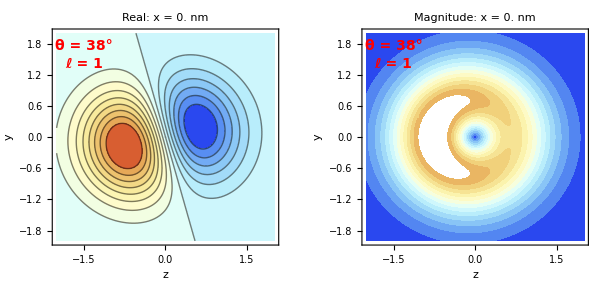

Here is a 3-D view of the absolute value of the E-field cross section.

-Graphics3D-

Despite this, the interference patterns in region 2 indicate that OAM is conserved. This is surprising given that the linear momentum is not conserved across the interface.

-Graphics-

-Graphics-

## Two Interfaces and Frustrated Internal Reflection

Evaluate jump conditions at x = y = 0 and t = 0 at two interface locations:  z = 0,  z = L .

### TE Polarization: Derivation of E-field Terms

⟦E_y⟧=0

⟦√ϵ E_y(k̂)_z⟧=0

E_i(r⃗, t) =  E_i  ⅇ^(ⅈ (k⃗·r⃗-ω t))ŷ

E_r(r⃗, t) =  E_r  ⅇ^(ⅈ (k⃗·r⃗-ω t))ŷ

E_t(r⃗, t) =  E_t  ⅇ^(ⅈ (k⃗·r⃗-ω t))ŷ

```mathematica
Clear[θ,θ2,θ3,ϵ1,ϵ2,ϵ3];

θ2[θ_,ϵ1_,ϵ2_,ϵ3_]=ArcSin[√(ϵ1/ϵ2)Sin[θ]];

θ3[θ_,ϵ1_,ϵ2_,ϵ3_]=ArcSin[√(ϵ2/ϵ3)Sin[θ2[θ,ϵ1,ϵ2,ϵ3]]];
```

```mathematica
Clear[ki1,kr1,kr2,kt2,rvec,x,y,z];

ki1[θ_,ϵ1_,ϵ2_,ϵ3_]={Sin[θ],0,Cos[θ]};
kr1[θ_,ϵ1_,ϵ2_,ϵ3_]={Sin[θ],0,-Cos[θ]};
kt1[θ_,ϵ1_,ϵ2_,ϵ3_]={Sin[θ2[θ,ϵ1,ϵ2,ϵ3]],0,Cos[θ2[θ,ϵ1,ϵ2,ϵ3]]};
kr2[θ_,ϵ1_,ϵ2_,ϵ3_]={Sin[θ2[θ,ϵ1,ϵ2,ϵ3]],0,-Cos[θ2[θ,ϵ1,ϵ2,ϵ3]]};
kt2[θ_,ϵ1_,ϵ2_,ϵ3_]={Sin[θ3[θ,ϵ1,ϵ2,ϵ3]],0,Cos[θ3[θ,ϵ1,ϵ2,ϵ3]]};

rvec[x_,y_,z_]={x,y,z};
```

```mathematica
Simplify[Solve[θ2[θ,ϵ1,1,ϵ1]==π/2,θ],{θ>0,θ<π/2}]
```

```mathematica
Simplify[Simplify[Solve[θ2[θ,ϵ1,ϵ2,ϵ1]==π/2,θ],{θ>0,θ<π/2,Element[C[1],Integers]}]/. C[1]->0,{ϵ1>0,ϵ2>0}]
```

```mathematica
θcrit[ϵ1_,ϵ2_]=ArcSin[√(ϵ2/ϵ1)];
```

```mathematica
Plot[θcrit[ϵ1,1]/Degree,{ϵ1,1,6},PlotStyle->{Thick, Darker[Red]},Filling->Axis,Frame->True,GridLines->Automatic,FrameLabel->{coloredfont["ϵ_1",14,Black],coloredfont["θ_crit (Deg)",14,Black]},PlotLabel->coloredfont["Critical Angle",18,Black]]
```

We therefore know the angles and can solve the 4 equations for the 4 unknowns that we have after setting EiB1 = 1 i.e. ErB1, EtB1, ErB2, EtB2.

In the analysis below, the characteristic length is taken to be 1/k_1. It is relevant that k_2/k_1=√(ϵ_2/ϵ_1)  as shown below ...

c = ω/k = 1/(√(μ μ_0 ϵ ϵ_0))

Therefore

k = ω √(μ μ_0 ϵ ϵ_0)

k_2/k_1 = √(ϵ_2/ϵ_1)

This term appears in the exponents of the third and fourth jump conditions below:

```mathematica
sol=Simplify[Solve[{
1 + ErB1 ==EtB1 + ErB2,
√ϵ1(1 -ErB1) Cos[θ1] == √ϵ2(EtB1 - ErB2)Cos[θ2] ,

EtB1 Exp[ⅈ √(ϵ2/ϵ1)kt1[θ,ϵ1,ϵ2,ϵ3].rvec[0,0,L]] + ErB2 Exp[ⅈ √(ϵ2/ϵ1) kr2[θ,ϵ1,ϵ2,ϵ3].rvec[0,0,L]] == EtB2 Exp[ⅈ kt2[θ,ϵ1,ϵ2,ϵ3].rvec[0,0,L]],

√ϵ2(EtB1 Exp[ⅈ √(ϵ2/ϵ1)kt1[θ,ϵ1,ϵ2,ϵ3].rvec[0,0,L]] - ErB2 Exp[ⅈ √(ϵ2/ϵ1)kr2[θ,ϵ1,ϵ2,ϵ3].rvec[0,0,L]]) Cos[θ2] == √ϵ3(EtB2 Exp[ⅈ kt2[θ,ϵ1,ϵ2,ϵ3].rvec[0,0,L]])Cos[θ3] 


},{ErB1, EtB1, ErB2, EtB2}]];
```

```mathematica
Clear[EtB1$TE];

ErB1$TE[θ_,ϵ1_,ϵ2_,ϵ3_] = Simplify[ErB1 /. sol[[1]] /. {θ1->θ, θ2->θ2[θ,ϵ1,ϵ2,ϵ3], θ3->θ3[θ,ϵ1,ϵ2,ϵ3]}];

EtB1$TE[θ_,ϵ1_,ϵ2_,ϵ3_] = Simplify[EtB1 /. sol[[1]]  /. {θ1->θ, θ2->θ2[θ,ϵ1,ϵ2,ϵ3], θ3->θ3[θ,ϵ1,ϵ2,ϵ3]}];

ErB2$TE[θ_,ϵ1_,ϵ2_,ϵ3_] = Simplify[ErB2 /. sol[[1]]  /. {θ1->θ, θ2->θ2[θ,ϵ1,ϵ2,ϵ3], θ3->θ3[θ,ϵ1,ϵ2,ϵ3]}];

EtB2$TE[θ_,ϵ1_,ϵ2_,ϵ3_] = Simplify[EtB2 /. sol[[1]]  /. {θ1->θ, θ2->θ2[θ,ϵ1,ϵ2,ϵ3], θ3->θ3[θ,ϵ1,ϵ2,ϵ3]}];
```

```mathematica
Simplify[ErB1$TE[θ,ϵ1,n^2 ϵ1,n^2 ϵ1],{ϵ1>0,n>0}]
```

```mathematica
Clear[EiB1$TE$func,ErB1$TE$func,EtB1$TE$func,ErB2$TE$func,EtB2$TE$func];

EiB1$TE$func[θ_,ϵ1_,ϵ2_,ϵ3_,x_,z_,L_]=Exp[ⅈ ki1[θ,ϵ1,ϵ2,ϵ3].rvec[x,0,z]];
ErB1$TE$func[θ_,ϵ1_,ϵ2_,ϵ3_,x_,z_,L_]=ErB1$TE[θ,ϵ1,ϵ2,ϵ3]Exp[ⅈ kr1[θ,ϵ1,ϵ2,ϵ3].rvec[x,0,z]];
EtB1$TE$func[θ_,ϵ1_,ϵ2_,ϵ3_,x_,z_,L_]=EtB1$TE[θ,ϵ1,ϵ2,ϵ3]Exp[ⅈ kt1[θ,ϵ1,ϵ2,ϵ3].rvec[x,0,z]];
ErB2$TE$func[θ_,ϵ1_,ϵ2_,ϵ3_,x_,z_,L_]=ErB2$TE[θ,ϵ1,ϵ2,ϵ3]Exp[ⅈ kr2[θ,ϵ1,ϵ2,ϵ3].rvec[x,0,z-L]];
EtB2$TE$func[θ_,ϵ1_,ϵ2_,ϵ3_,x_,z_,L_]=EtB2$TE[θ,ϵ1,ϵ2,ϵ3]Exp[ⅈ kt2[θ,ϵ1,ϵ2,ϵ3].rvec[x,0,z-L]];
```

```mathematica
FullSimplify[Simplify[EtB2$TE[θ,ϵ1,ϵ2,ϵ1],{ϵ1>0,ϵ2>0}]/. ϵ2->n^2 ϵ1,{ϵ1>0,n>0,θ>0,θ<π/2}]
```

### TM Polarization: Derivation of E-field Terms

⟦E_x⟧=0

⟦ϵ E⃗⟧·n̂=0

E_i(r⃗, t) =  E_i Cos[θ] ⅇ^(ⅈ (k⃗·r⃗-ω t))x̂ + E_i Sin[θ] ⅇ^(ⅈ (k⃗·r⃗-ω t))ẑ

E_r(r⃗, t) =  E_r Cos[θ] ⅇ^(ⅈ (k⃗·r⃗-ω t))x̂ -  E_r Sin[θ] ⅇ^(ⅈ (k⃗·r⃗-ω t))ẑ

E_t(r⃗, t) =  E_t Cos[θ_2] ⅇ^(ⅈ (k⃗·r⃗-ω t))x̂ -  E_t Sin[θ_2] ⅇ^(ⅈ (k⃗·r⃗-ω t))ẑ

```mathematica
Clear[θ2,θ3];

θ2[θ_,ϵ1_,ϵ2_,ϵ3_]=ArcSin[√(ϵ1/ϵ2)Sin[θ]];

θ3[θ_,ϵ1_,ϵ2_,ϵ3_]=ArcSin[√(ϵ2/ϵ3)Sin[θ2[θ,ϵ1,ϵ2,ϵ3]]];
```

```mathematica
Clear[ki1,kr1,kr2,kt2,rvec,x,y,z];

ki1[θ_,ϵ1_,ϵ2_,ϵ3_]={Sin[θ],0,Cos[θ]};
kr1[θ_,ϵ1_,ϵ2_,ϵ3_]={Sin[θ],0,-Cos[θ]};
kt1[θ_,ϵ1_,ϵ2_,ϵ3_]={Sin[θ2[θ,ϵ1,ϵ2,ϵ3]],0,Cos[θ2[θ,ϵ1,ϵ2,ϵ3]]};
kr2[θ_,ϵ1_,ϵ2_,ϵ3_]={Sin[θ2[θ,ϵ1,ϵ2,ϵ3]],0,-Cos[θ2[θ,ϵ1,ϵ2,ϵ3]]};
kt2[θ_,ϵ1_,ϵ2_,ϵ3_]={Sin[θ3[θ,ϵ1,ϵ2,ϵ3]],0,Cos[θ3[θ,ϵ1,ϵ2,ϵ3]]};


rvec[x_,y_,z_]={x,y,z};
```

We therefore know the angles and can solve the 4 equations for the 4 unknowns that we have after setting EiB1 = 1 i.e. ErB1, EtB1, ErB2, EtB2.

```mathematica
rvec[0,0,L]
```

```mathematica
Clear[ErB1, EtB1, ErB2, EtB2,sol];

sol=Simplify[Solve[{
(1  + ErB1 )Cos[θ1] == (EtB1+ErB2) Cos[θ2],
ϵ1(1  - ErB1 )Sin[θ1] ==ϵ2 (EtB1-ErB2) Sin[θ2],

(EtB1 Exp[ⅈ √(ϵ2/ϵ1)kt1[θ,ϵ1,ϵ2,ϵ3].rvec[0,0,L]] + ErB2 Exp[ⅈ √(ϵ2/ϵ1)kr2[θ,ϵ1,ϵ2,ϵ3].rvec[0,0,L]])Cos[θ2] == EtB2 Exp[ⅈ kt2[θ,ϵ1,ϵ2,ϵ3].rvec[0,0,L]] Cos[θ3],

ϵ2(EtB1 Exp[ⅈ √(ϵ2/ϵ1)kt1[θ,ϵ1,ϵ2,ϵ3].rvec[0,0,L]]  - ErB2 Exp[ⅈ √(ϵ2/ϵ1)kr2[θ,ϵ1,ϵ2,ϵ3].rvec[0,0,L]] )Sin[θ2] ==ϵ3 EtB2 Exp[ⅈ kt2[θ,ϵ1,ϵ2,ϵ3].rvec[0,0,L]] Sin[θ3]

},{ErB1, EtB1, ErB2, EtB2}]];
```

```mathematica
Clear[EtB1$TM];

ErB1$TM[θ_,ϵ1_,ϵ2_,ϵ3_] = Simplify[ErB1 /. sol[[1]] /. {θ1->θ, θ2->θ2[θ,ϵ1,ϵ2,ϵ3], θ3->θ3[θ,ϵ1,ϵ2,ϵ3]}];

EtB1$TM[θ_,ϵ1_,ϵ2_,ϵ3_] = Simplify[EtB1 /. sol[[1]]  /. {θ1->θ, θ2->θ2[θ,ϵ1,ϵ2,ϵ3], θ3->θ3[θ,ϵ1,ϵ2,ϵ3]}];

ErB2$TM[θ_,ϵ1_,ϵ2_,ϵ3_] = Simplify[ErB2 /. sol[[1]]  /. {θ1->θ, θ2->θ2[θ,ϵ1,ϵ2,ϵ3], θ3->θ3[θ,ϵ1,ϵ2,ϵ3]}];

EtB2$TM[θ_,ϵ1_,ϵ2_,ϵ3_] = Simplify[EtB2 /. sol[[1]]  /. {θ1->θ, θ2->θ2[θ,ϵ1,ϵ2,ϵ3], θ3->θ3[θ,ϵ1,ϵ2,ϵ3]}];
```

```mathematica
FullSimplify[ErB2$TM[θ,ϵ1,n^2 ϵ1,n^2 ϵ1],{ϵ1>0,n>0,θ>0,θ<π/2}]
```

```mathematica
FullSimplify[ErB1$TM[θ,ϵ1,n^2 ϵ1,n^2 ϵ1],{ϵ1>0,n>0,θ>0,θ<π/2}]
```

```mathematica
FullSimplify[(Sin[θ]^2+n^2 (-1+Cos[θ] √(n^2-Sin[θ]^2)))/(Sin[θ]^2-n^2 (1+Cos[θ] √(n^2-Sin[θ]^2)))-(-n^2 Cos[θ]+√(n^2-Sin[θ]^2))/(n^2 Cos[θ]+√(n^2-Sin[θ]^2))]
```

(-n^2 Cos[θ]+√(n^2-Sin[θ]^2))/(n^2 Cos[θ]+√(n^2-Sin[θ]^2))

```mathematica
Simplify[ErB1$TE[θ,ϵ1,n^2 ϵ1,n^2 ϵ1],{ϵ1>0,n>0}]
```

```mathematica
Clear[EiB1$TM$func,ErB1$TM$func,EtB1$TM$func,ErB2$TM$func,EtB2$TM$func];

EiB1$TM$func[θ_,ϵ1_,ϵ2_,ϵ3_,x_,z_,L_]=Exp[ⅈ ki1[θ,ϵ1,ϵ2,ϵ3].rvec[x,0,z]];
ErB1$TM$func[θ_,ϵ1_,ϵ2_,ϵ3_,x_,z_,L_]=ErB1$TM[θ,ϵ1,ϵ2,ϵ3]Exp[ⅈ kr1[θ,ϵ1,ϵ2,ϵ3].rvec[x,0,z]];
EtB1$TM$func[θ_,ϵ1_,ϵ2_,ϵ3_,x_,z_,L_]=EtB1$TM[θ,ϵ1,ϵ2,ϵ3]Exp[ⅈ kt1[θ,ϵ1,ϵ2,ϵ3].rvec[x,0,z]];
ErB2$TM$func[θ_,ϵ1_,ϵ2_,ϵ3_,x_,z_,L_]=ErB2$TM[θ,ϵ1,ϵ2,ϵ3]Exp[ⅈ kr2[θ,ϵ1,ϵ2,ϵ3].rvec[x,0,z-L]];
EtB2$TM$func[θ_,ϵ1_,ϵ2_,ϵ3_,x_,z_,L_]=EtB2$TM[θ,ϵ1,ϵ2,ϵ3]Exp[ⅈ kt2[θ,ϵ1,ϵ2,ϵ3].rvec[x,0,z-L]];
```

### Application 1

```mathematica
Clear[p$TE$contours,p$B1,p$B2,xmax,xmin,zmax,zmin];

xmax = 10;xmin = -xmax;

Lset = 4.0;
zmin = -3.0;zmax = -zmin + Lset;

p$B1=Show[Graphics[{White,Thickness[.01],Line[{{0,xmin},{0,xmax}}]}]];
p$B2=Show[Graphics[{White,Thickness[.01],Line[{{Lset,xmin},{Lset,xmax}}]}]];

θset = 35 Degree;
ϵ1set = 4.0; ϵ2set = 1.0;ϵ3set = ϵ1set;

p$TE$contours = ContourPlot[Which[
z≤ 0,Re[EiB1$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
z≤ Lset,Re[EtB1$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]+0ErB2$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
True,Re[EtB2$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]]
],{z,zmin,zmax},{x,xmin,xmax},Contours->20,ColorFunction->"TemperatureMap",PlotRange->All,FrameLabel->{font["z",14],font["x",14]},PlotLabel->coloredfont["TE Polarization",14,Blue],PlotPoints->50];

Show[p$TE$contours,p$B1,p$B2]
```

```mathematica
Plot3D[Which[
z≤ 0,Re[EiB1$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
z≤ Lset,Re[EtB1$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]+0ErB2$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
True,Re[EtB2$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]]
],{z,zmin,zmax},{x,xmin,xmax},ColorFunction->"TemperatureMap",PlotRange->All,PlotLabel->coloredfont["TE Polarization",14,Blue],PlotPoints->50]
```

```mathematica
Clear[p$TM$contours,p$B1,p$B2,p$TM$contours];

p$B1=Show[Graphics[{White,Thickness[.01],Line[{{0,xmin},{0,xmax}}]}]];
p$B2=Show[Graphics[{White,Thickness[.01],Line[{{Lset,xmin},{Lset,xmax}}]}]];

p$TM$contours = ContourPlot[Which[
z≤ 0,Re[EiB1$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
z≤ Lset,Re[EtB1$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]+0ErB2$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
True,Re[EtB2$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]]
],{z,zmin,zmax},{x,xmin,xmax},Contours->20,ColorFunction->"TemperatureMap",PlotRange->All,FrameLabel->{font["z",14],font["x",14]},PlotLabel->coloredfont["TM Polarization",14,Blue],PlotPoints->50];

Show[p$TM$contours,p$B1,p$B2]
```

Here is a way of visualizing the relative amplitude of the propagating wave in region 3 as a function of ϵ1, the critical angle, and the layer thickness.

```mathematica
Clear[TE$func,TM$func];

TE$func[θ_,ϵ1_,L_] = Abs[Abs[EtB2$TE$func[θ Degree,ϵ1,1,ϵ1,0,L,L]]/Abs[EiB1$TE$func[θ Degree,ϵ1,1,ϵ1,0,0,L]]];
TM$func[θ_,ϵ1_,L_] = Abs[Abs[EtB2$TM$func[θ Degree,ϵ1,1,ϵ1,0,L,L]]/Abs[EiB1$TM$func[θ Degree,ϵ1,1,ϵ1,0,0,L]]];
```

```mathematica
ϵ1set = 2;

p$TE=ContourPlot[TE$func[θ,ϵ1set,L],{L,1,5},{θ,θcrit[ϵ1set]/Degree ,75 },BaseStyle->{Black,18},ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),PlotRange->All,PlotLegends->Automatic,ImageSize->500,PlotLabel->"TE Ratio: ϵ_1 = "<>ToString[ϵ1set],FrameLabel->{"Spacing, L","Incident Angle, θ_1 (deg)"}]

p$TM=ContourPlot[TM$func[θ,ϵ1set,L],{L,1,5},{θ,θcrit[ϵ1set]/Degree ,75 },BaseStyle->{Black,18},ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),PlotRange->All,PlotLegends->Automatic,ImageSize->500,PlotLabel->"TM Ratio: ϵ_1 = "<>ToString[ϵ1set],FrameLabel->{"Spacing, L","Incident Angle, θ_1 (deg)"}]
```

```mathematica
ϵ1set = 4;

p$TE=ContourPlot[TE$func[θ,ϵ1set,L],{L,1,5},{θ,θcrit[ϵ1set]/Degree ,75 },BaseStyle->{Black,18},ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),PlotRange->All,PlotLegends->Automatic,ImageSize->500,PlotLabel->"TE Ratio: ϵ_1 = "<>ToString[ϵ1set],FrameLabel->{"Spacing, L","Incident Angle, θ_1 (deg)"}]

p$TM=ContourPlot[TM$func[θ,ϵ1set,L],{L,1,5},{θ,θcrit[ϵ1set]/Degree ,75 },BaseStyle->{Black,18},ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),PlotRange->All,PlotLegends->Automatic,ImageSize->500,PlotLabel->"TM Ratio: ϵ_1 = "<>ToString[ϵ1set],FrameLabel->{"Spacing, L","Incident Angle, θ_1 (deg)"}]
```

```mathematica
ϵ1set = 6;

p$TE=ContourPlot[TE$func[θ,ϵ1set,L],{L,1,5},{θ,θcrit[ϵ1set]/Degree ,75 },BaseStyle->{Black,18},ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),PlotRange->All,PlotLegends->Automatic,ImageSize->500,PlotLabel->"TE Ratio: ϵ_1 = "<>ToString[ϵ1set],FrameLabel->{"Spacing, L","Incident Angle, θ_1 (deg)"}]

p$TM=ContourPlot[TM$func[θ,ϵ1set,L],{L,1,5},{θ,θcrit[ϵ1set]/Degree ,75 },BaseStyle->{Black,18},ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),PlotRange->All,PlotLegends->Automatic,ImageSize->500,PlotLabel->"TM Ratio: ϵ_1 = "<>ToString[ϵ1set],FrameLabel->{"Spacing, L","Incident Angle, θ_1 (deg)"}]
```

### Application 2

```mathematica
θcrit[2.]/Degree
```

```mathematica
θcrit[ϵ1_]=ArcSin[1/√(ϵ1/ϵ2)];
```

```mathematica
Clear[p$TE$contours,p$B1,p$B2,xmax,xmin,zmax,zmin];

xmax = 10;xmin = -xmax;

Lset = 4.0;
zmin = -3.0;zmax = -zmin + Lset;

p$B1=Show[Graphics[{White,Thickness[.01],Line[{{0,xmin},{0,xmax}}]}]];
p$B2=Show[Graphics[{White,Thickness[.01],Line[{{Lset,xmin},{Lset,xmax}}]}]];

θset = 46 Degree;
ϵ1set = 2.0; ϵ2set = 1.0;ϵ3set = ϵ1set;

p$TE$contours = ContourPlot[Which[
z≤ 0,Re[EiB1$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
z≤ Lset,Re[EtB1$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]+0ErB2$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
True,Re[EtB2$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]]
],{z,zmin,zmax},{x,xmin,xmax},Contours->20,ColorFunction->"TemperatureMap",PlotRange->All,FrameLabel->{font["z",14],font["x",14]},PlotLabel->coloredfont["TE Polarization",14,Blue],PlotPoints->50];

Show[p$TE$contours,p$B1,p$B2]
```

```mathematica
Plot3D[Which[
z≤ 0,Re[EiB1$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
z≤ Lset,Re[EtB1$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]+0ErB2$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
True,Re[EtB2$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]]
],{z,zmin,zmax},{x,xmin,xmax},ColorFunction->"TemperatureMap",PlotRange->All,PlotLabel->coloredfont["TE Polarization",14,Blue],PlotPoints->50]
```

```mathematica
Clear[p$TM$contours,p$B1,p$B2,p$TM$contours];

p$B1=Show[Graphics[{White,Thickness[.01],Line[{{0,xmin},{0,xmax}}]}]];
p$B2=Show[Graphics[{White,Thickness[.01],Line[{{Lset,xmin},{Lset,xmax}}]}]];

p$TM$contours = ContourPlot[Which[
z≤ 0,Re[EiB1$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
z≤ Lset,Re[EtB1$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]+0ErB2$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
True,Re[EtB2$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]]
],{z,zmin,zmax},{x,xmin,xmax},Contours->20,ColorFunction->"TemperatureMap",PlotRange->All,FrameLabel->{font["z",14],font["x",14]},PlotLabel->coloredfont["TM Polarization",14,Blue],PlotPoints->50];

Show[p$TM$contours,p$B1,p$B2]
```

Here is a way of visualizing the relative amplitude of the propagating wave in region 3 as a function of ϵ1, the critical angle, and the layer thickness.

```mathematica
θcrit[ϵ1set]
```

```mathematica
EtB2$TE$func[θ Degree,ϵ1,1,ϵ1,0,L,L] /. ϵ1->ϵ1set
```

```mathematica
Clear[TE$func,TM$func];

TE$func[θ_,ϵ1_,L_] = Abs[Abs[EtB2$TE$func[θ Degree,ϵ1,1,ϵ1,0,L,L]]/Abs[EiB1$TE$func[θ Degree,ϵ1,1,ϵ1,0,0,L]]];
TM$func[θ_,ϵ1_,L_] = Abs[Abs[EtB2$TM$func[θ Degree,ϵ1,1,ϵ1,0,L,L]]/Abs[EiB1$TM$func[θ Degree,ϵ1,1,ϵ1,0,0,L]]];
```

```mathematica
ϵ1set = 2;

p$TE=ContourPlot[TE$func[θ,ϵ1set,L],{L,1,5},{θ,θcrit[ϵ1set,1]/Degree ,75 },BaseStyle->{Black,18},ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),PlotRange->All,PlotLegends->Automatic,ImageSize->500,PlotLabel->"TE Ratio: ϵ_1 = "<>ToString[ϵ1set],FrameLabel->{"Spacing, L","Incident Angle, θ_1 (deg)"}]

p$TM=ContourPlot[TM$func[θ,ϵ1set,L],{L,1,5},{θ,θcrit[ϵ1set,1]/Degree ,75 },BaseStyle->{Black,18},ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),PlotRange->All,PlotLegends->Automatic,ImageSize->500,PlotLabel->"TM Ratio: ϵ_1 = "<>ToString[ϵ1set],FrameLabel->{"Spacing, L","Incident Angle, θ_1 (deg)"}]
```

```mathematica
ϵ1set = 4;

p$TE=ContourPlot[TE$func[θ,ϵ1set,L],{L,1,5},{θ,θcrit[ϵ1set,1]/Degree ,75 },BaseStyle->{Black,18},ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),PlotRange->All,PlotLegends->Automatic,ImageSize->500,PlotLabel->"TE Ratio: ϵ_1 = "<>ToString[ϵ1set],FrameLabel->{"Spacing, L","Incident Angle, θ_1 (deg)"}]

p$TM=ContourPlot[TM$func[θ,ϵ1set,L],{L,1,5},{θ,θcrit[ϵ1set,1]/Degree ,75 },BaseStyle->{Black,18},ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),PlotRange->All,PlotLegends->Automatic,ImageSize->500,PlotLabel->"TM Ratio: ϵ_1 = "<>ToString[ϵ1set],FrameLabel->{"Spacing, L","Incident Angle, θ_1 (deg)"}]
```

```mathematica
ϵ1set = 6;

p$TE=ContourPlot[TE$func[θ,ϵ1set,L],{L,1,5},{θ,θcrit[ϵ1set,1]/Degree ,75 },BaseStyle->{Black,18},ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),PlotRange->All,PlotLegends->Automatic,ImageSize->500,PlotLabel->"TE Ratio: ϵ_1 = "<>ToString[ϵ1set],FrameLabel->{"Spacing, L","Incident Angle, θ_1 (deg)"}]

p$TM=ContourPlot[TM$func[θ,ϵ1set,L],{L,1,5},{θ,θcrit[ϵ1set,1]/Degree ,75 },BaseStyle->{Black,18},ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),PlotRange->All,PlotLegends->Automatic,ImageSize->500,PlotLabel->"TM Ratio: ϵ_1 = "<>ToString[ϵ1set],FrameLabel->{"Spacing, L","Incident Angle, θ_1 (deg)"}]
```

### Application 3

```mathematica
θ2[θ_,ϵ1_,ϵ2_,ϵ3_]=ArcSin[√(ϵ1/ϵ2)Sin[θ]];

θ3[θ_,ϵ1_,ϵ2_,ϵ3_]=ArcSin[√(ϵ2/ϵ3)Sin[θ2[θ,ϵ1,ϵ2,ϵ3]]];
```

```mathematica
Sin[30 Degree]
```

```mathematica
θ3[30 Degree,4,2,1]/Degree//N
```

```mathematica
EtB1$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]
```

```mathematica
Clear[p$B1,p$B2,xmax,xmin,zmax,zmin];

xmax = 10;xmin = -xmax;

Lset = 6.0;
zmin = -3.0;zmax = -zmin + Lset;

p$B1=Show[Graphics[{White,Thickness[.01],Line[{{0,xmin},{0,xmax}}]}]];
p$B2=Show[Graphics[{White,Thickness[.01],Line[{{Lset,xmin},{Lset,xmax}}]}]];

θset = 70 Degree;
ϵ1set = 1.0; ϵ2set = 2.0;ϵ3set = 8.0;

p1 = ContourPlot[Which[
z≤ 0,Re[EiB1$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
z≤ Lset,Re[EtB1$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]+0ErB2$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
True,Re[EtB2$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]]
],{z,zmin,zmax},{x,xmin,xmax},Contours->20,ColorFunction->"TemperatureMap",PlotRange->All,FrameLabel->{font["z",14],font["x",14]},PlotLabel->coloredfont["TE Polarization",14,Blue],PlotPoints->50];

p2 = ContourPlot[Which[
z≤ 0,Re[ErB1$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
z≤ Lset,Re[ErB2$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]+0ErB2$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
True,Re[EtB2$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]]
],{z,zmin,zmax},{x,xmin,xmax},Contours->20,ColorFunction->"TemperatureMap",PlotRange->All,FrameLabel->{font["z",14],font["x",14]},PlotLabel->coloredfont["TE Polarization",14,Blue],PlotPoints->50];



GraphicsRow[{Show[p1,p$B1,p$B2],Show[p2,p$B1,p$B2]},ImageSize->500]
```

-Graphics-

-Graphics-

```mathematica
Clear[p$TM$contours,p$B1,p$B2,p$TM$contours];

p$B1=Show[Graphics[{White,Thickness[.01],Line[{{0,xmin},{0,xmax}}]}]];
p$B2=Show[Graphics[{White,Thickness[.01],Line[{{Lset,xmin},{Lset,xmax}}]}]];

p$TM$contours = ContourPlot[Which[
z≤ 0,Re[EiB1$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
z≤ Lset,Re[EtB1$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]+0ErB2$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
True,Re[EtB2$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]]
],{z,zmin,zmax},{x,xmin,xmax},Contours->20,ColorFunction->"TemperatureMap",PlotRange->All,FrameLabel->{font["z",14],font["x",14]},PlotLabel->coloredfont["TM Polarization",14,Blue],PlotPoints->50];

Show[p$TM$contours,p$B1,p$B2]
```

### Application 4

```mathematica
kt1[θset,ϵ1set,ϵ2set,ϵ3set]
```

```mathematica
kt1[θ,ϵ1,ϵ2,ϵ3]
```

```mathematica
Clear[char$decay$length];

char$decay$length[θ_,ϵ1_,ϵ2_] = FullSimplify[1/√((ϵ1 Sin[θ]^2)/ϵ2-1),{θ>0,θ<π/2,ϵ1>0,ϵ2>0}]
```

```mathematica
char$decay$length[35.0 Degree, 4.0,1.0]
```

```mathematica
Chop[char$decay$length[θset,ϵ1set,ϵ2set]]
```

```mathematica
√(ϵ2set/ϵ1set)
```

```mathematica
θcrit[ϵ1_,ϵ2_]=ArcSin[√(ϵ2/ϵ1)];
```

```mathematica
θ2[θ_,ϵ1_,ϵ2_,ϵ3_]=ArcSin[√(ϵ1/ϵ2)Sin[θ]];

θ3[θ_,ϵ1_,ϵ2_,ϵ3_]=ArcSin[√(ϵ2/ϵ3)Sin[θ2[θ,ϵ1,ϵ2,ϵ3]]];
```

```mathematica
Sin[30 Degree]
```

```mathematica
θ3[30 Degree,4,2,1]/Degree//N
```

```mathematica
EtB1$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,0,Lset,Lset]
```

```mathematica
θcrit[ϵ1set,ϵ2set]/Degree
```

```mathematica
Clear[p$B1,p$B2,xmax,xmin,zmax,zmin];

xmax = 10;xmin = -xmax;

Lset = 5.0;
zmin = -3.0;zmax = -zmin + Lset;

p$B1=Show[Graphics[{White,Thickness[.01],Line[{{0,xmin},{0,xmax}}]}]];
p$B2=Show[Graphics[{White,Thickness[.01],Line[{{Lset,xmin},{Lset,xmax}}]}]];

θset = 35.0 Degree;
ϵ1set = 4.0; ϵ2set = 1.0;ϵ3set = 4.0;

p1 = ContourPlot[Which[
z≤ 0,Re[EiB1$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
z≤ Lset,Re[EtB1$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]+0ErB2$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
True,Re[EtB2$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]]
],{z,zmin,zmax},{x,xmin,xmax},Contours->20,ColorFunction->"TemperatureMap",PlotRange->All,FrameLabel->{font["z",14],font["x",14]},PlotLabel->coloredfont["TE Polarization",14,Blue],PlotPoints->50];

p2 = ContourPlot[Which[
z≤ 0,Re[ErB1$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
z≤ Lset,Re[ErB2$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]+0ErB2$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
True,Re[EtB2$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]]
],{z,zmin,zmax},{x,xmin,xmax},Contours->20,ColorFunction->"TemperatureMap",PlotRange->All,FrameLabel->{font["z",14],font["x",14]},PlotLabel->coloredfont["TE Polarization",14,Blue],PlotPoints->50];



GraphicsRow[{Show[p1,p$B1,p$B2],Show[p2,p$B1,p$B2]},ImageSize->500]
```

```mathematica
Clear[p$TM$contours,p$B1,p$B2,p$TM$contours];

p$B1=Show[Graphics[{White,Thickness[.01],Line[{{0,xmin},{0,xmax}}]}]];
p$B2=Show[Graphics[{White,Thickness[.01],Line[{{Lset,xmin},{Lset,xmax}}]}]];

p1 = ContourPlot[Which[
z≤ 0,Re[EiB1$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
z≤ Lset,Re[EtB1$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]+0ErB2$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
True,Re[EtB2$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]]
],{z,zmin,zmax},{x,xmin,xmax},Contours->20,ColorFunction->"TemperatureMap",PlotRange->All,FrameLabel->{font["z",14],font["x",14]},PlotLabel->coloredfont["TM Polarization",14,Blue],PlotPoints->50];

p2 = ContourPlot[Which[
z≤ 0,Re[ErB1$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
z≤ Lset,Re[ErB2$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]+0ErB2$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
True,Re[EtB2$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]]
],{z,zmin,zmax},{x,xmin,xmax},Contours->20,ColorFunction->"TemperatureMap",PlotRange->All,FrameLabel->{font["z",14],font["x",14]},PlotLabel->coloredfont["TM Polarization",14,Blue],PlotPoints->50];

GraphicsRow[{Show[p1,p$B1,p$B2],Show[p2,p$B1,p$B2]},ImageSize->500]
```

```mathematica
Clear[R1,R2,T1,T2,θ,n];

R2=(Cos[θ]-√(n^2-Sin[θ]^2))/(Cos[θ]+√(n^2-Sin[θ]^2)) ;  (* Fresnel Reflection Coefficient: s/TE *)

R1=(-n^2 Cos[θ]+√(n^2-Sin[θ]^2))/(n^2 Cos[θ]+√(n^2-Sin[θ]^2));(* Fresnel Reflection Coefficient: p/TM *)

T2=Simplify[(2Cos[θ])/(Cos[θ]+√(n^2-Sin[θ]^2))];(* Fresnel Transmission Coefficient: s/TE *)

T1=Simplify[(2n Cos[θ])/(n^2 Cos[θ]+√(n^2-Sin[θ]^2))];(* Fresnel Transmission Coefficient: p/TM *)
```

```mathematica
R1 /. {n->√(ϵ2set/ϵ1set),θ->θset}

Chop[Simplify[ErB1$TM$func[θset,ϵ1set,ϵ2set,ϵ2set,0,0,L]]]

ErB1$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,0,0,∞]
```

```mathematica
Plot[Re[ErB1$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,0,0,L]],{L,.1,20}]
```

```mathematica
R2 /. {n->√(ϵ2set/ϵ1set),θ->θset}

Chop[Simplify[ErB1$TE$func[θset,ϵ1set,ϵ2set,ϵ2set,0,0,L]]]

ErB1$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,0,0,∞]

Plot[Re[ErB1$TE$func[θset,ϵ1set,ϵ2set,ϵ3set,0,0,L]],{L,.1,30}]
```

```mathematica
Plot3D[Which[
z≤ 0,Re[EiB1$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
z≤ Lset,Re[EtB1$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]+0ErB2$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]],
True,Re[EtB2$TM$func[θset,ϵ1set,ϵ2set,ϵ3set,x,z,Lset]]
],{z,zmin,zmax},{x,xmin,xmax},ColorFunction->"TemperatureMap",PlotRange->All,PlotLabel->coloredfont["TM Polarization",14,Blue],PlotPoints->50]
```